# Legendre transform

```mathematica
Clear[F,gmax];
F[x_]:=(x^2-1)^2/4;
gmax[x_,p_]:=x p-F[x];
```

```mathematica
Clear[g,sols,dG,dG,sols,d2G,d2FEvaluated,x0,t,x0List]
```

```mathematica
gfun[pp_]:=Module[{p=pp,dG,sols,d2F,d2FEvaluated,x0,t,x0List},
Print["Setting p=",p];
dG=Evaluate[D[gmax[x,p],x]];
Print["Derivative dG/dx == ",dG,"== 0"];
sols=NSolve[dG==0,x];
Print["Solutions found: ",sols];
d2F=Evaluate[D[F[x],{x,2}]];
Print["Second derivative d^2F/dx^2 == ",d2F];
d2FEvaluated=Flatten[Simplify[d2F]/.{sols}];
Print["Second derivative evaluate at the solutions d^2F/dx^2 == ",d2FEvaluated];
x0List={};
Do[t=d2FEvaluated[[i]];
x0=x/.sols[[i]];
If[Re[t]>=0&&Im[t]==0,AppendTo[x0List,x0]],{i,1,Length[d2FEvaluated]}];
Print["The possible solutions are x0=",x0List];
plot1=Show[Plot[{x .1,F[x],D[F[xx],xx]/.{xx->x}},{x,-2,2},PlotLegends->{"xp","F[x]","F''[x]"}],ListPlot[Table[{x0List[[i]],0},{i,1,Length[x0List]}],PlotStyle->Red]];Print[plot1];
Max[gmax[x,p]/.{x->x0List}]]
```

Setting p=0.1

Derivative dG/dx == 0.1-x (-1+x^2)== 0

Solutions found: {{x→-0.945649},{x→-0.101031},{x→1.04668}}

Second derivative d^2F/dx^2 == 1/4 (8 x^2+4 (-1+x^2))

Second derivative evaluate at the solutions d^2F/dx^2 == {1.68276,-0.969378,2.28662}

The possible solutions are x0={-0.945649,1.04668}

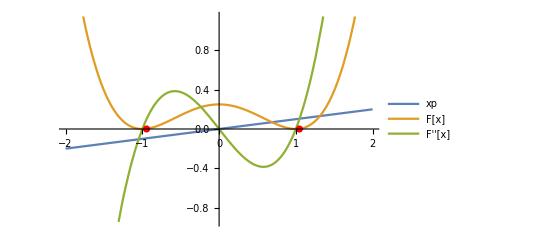

0.102386

```mathematica
gfun[.1]
```

```mathematica
gLegendre[pp_]:=Module[{p=pp,dG,sols,d2F,d2FEvaluated,x0,t,x0List},
dG=Evaluate[D[gmax[x,p],x]];
sols=NSolve[dG==0,x];
d2F=Evaluate[D[F[x],{x,2}]];
d2FEvaluated=Flatten[Simplify[d2F]/.{sols}];
x0List={};
Do[t=d2FEvaluated[[i]];
x0=x/.sols[[i]];
If[Re[t]>=0&&Im[t]==0,AppendTo[x0List,x0]],{i,1,Length[d2FEvaluated]}];
Max[gmax[x,p]/.{x->x0List}]]
```

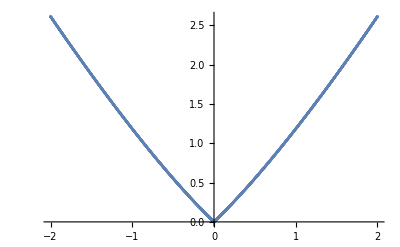

```mathematica
ListPlot[Table[{p,gLegendre[p]},{p,-2,2,.001}]]
```

# O(N) generators

Following formula 3.4 of https://arxiv.org/pdf/1605.03602.pdf

```mathematica
M[a_,b_,i_,j_]:=-I(KroneckerDelta[i,a]*KroneckerDelta[j,b]-KroneckerDelta[j,a]*KroneckerDelta[i,b])
```

```mathematica
M[a_,b_,NN_]:=Table[-I(KroneckerDelta[i,a]*KroneckerDelta[j,b]-KroneckerDelta[j,a]*KroneckerDelta[i,b]),{i,1,NN},{j,1,NN}]
```

Example: O(3) has three generators, namely M12, M23, M13.

Is is easy to show that Exp[i α M12] =Rz(α) generates a rotation along the z axis by an angle α .
Similarly M23 generates rotation along the x-axis and M13 along the y axis.

In this simple case M12 is the unbroken generator while M23 and M13 are broken generators, i.e., the vacuum is not symmetric under rotations along the x and y axis.

```mathematica
Clear[π1,π2];pionMatrix=I(π1 M[2,3,3]+π2 M[1,3,3]);Print[MatrixForm[pionMatrix]];
pionMatrix2=pionMatrix.pionMatrix;
(*π1=πtot Cos[pi];π2=πtot Sin[pi];*)
```

(0 | 0 | π2
0 | 0 | π1
-π2 | -π1 | 0)

```mathematica
MatrixForm[pionMatrix]
```

(0 | 0 | π2
0 | 0 | π1
-π2 | -π1 | 0)

```mathematica
Clear[X0];X0={0,0,1};
```

```mathematica
MatrixForm[DiagonalMatrix[{1,1,1}]+pionMatrix]
```

(1 | 0 | π2
0 | 1 | π1
-π2 | -π1 | 1)

```mathematica
MatrixForm[D[pionMatrix.pionMatrix/.{π1->π1[x],π2->π2[x]},x]]
```

(-2 π2[x] π2'[x] | -π2[x] π1'[x]-π1[x] π2'[x] | 0
-π2[x] π1'[x]-π1[x] π2'[x] | -2 π1[x] π1'[x] | 0
0 | 0 | -2 π1[x] π1'[x]-2 π2[x] π2'[x])

## Killing vectors for O(3)

see eqn. (4.21).

```mathematica
Clear[ϕvec,ϕvecPolar];
ϕvec={ϕ1,ϕ2,ϕ3};
ϕvecPolar=ϕvec/.{ϕ1->(f+h)Sin[θ]Cos[ϕ],ϕ2->(f+h)Sin[θ]Sin[ϕ],ϕ3->(f+h)Cos[θ]};
```

```mathematica
(**this is the general killing vector as shown in eqn. 4.21
The possible values of a, b correspond the generatos of O(3), 
namely (a,b)=(1,2),(1,3),(2,3)**)
tKilling[a_,b_]:=I M[a,b,3].ϕvec;
(**this is the gradient of the killing vector a,b with respect to the fields. neddec for the Lie bracket 4.27**)
DtKilling[a_,b_]:=Table[D[tKilling[a,b],{ϕ1,ϕ2,ϕ3}[[i]]],{i,1,3}];
```

Lets imagine we fix in eqn. 4.27 α=1 and β=2 then we get the following

```mathematica
α=1 ;
β=2;
```

```mathematica
M[1,2,3]
```

{{0,-ⅈ,0},{ⅈ,0,0},{0,0,0}}

```mathematica
listTKilling
```

{{ϕ2,-ϕ1,0},{ϕ3,0,-ϕ1},{0,ϕ3,-ϕ2}}

```mathematica
listTKilling={tKilling[1,2],tKilling[1,3],tKilling[2,3]};
listDtKilling={DtKilling[1,2],DtKilling[1,3],DtKilling[2,3]};
```

```mathematica
LieBracket[α_,β_]:=listTKilling[[α]].listDtKilling[[β]]-listTKilling[[β]].listDtKilling[[α]]
```

```mathematica
LieBracket[2,3]
```

{ϕ2,-ϕ1,0}

```mathematica
{listTKilling[[1]],listTKilling[[2]],listTKilling[[3]]}
```

{{ϕ2,-ϕ1,0},{ϕ3,0,-ϕ1},{0,ϕ3,-ϕ2}}

The Lie brackets are essentially a cross product where we have [t1,t2]=t3 corresponds to rx x ry = rz and so on. Thus

# Gegenbauer with BCs

```mathematica
NN=4;n=20;λ=(NN-1)/2;sol=DSolve[{G''[x]+2λ Cot[x]G'[x]+n(n+2λ)G[x]==0,G[π/2]==0.1,G'[π/2]==10},G[x],x];
Clear[Gegenbauer];Gegenbauer[xx_?NumericQ]:=(G[x]/.sol[[1]])/.{x->xx};
```

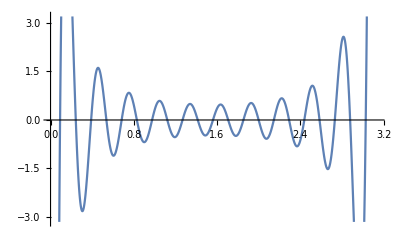

```mathematica
Plot[Gegenbauer[x],{x,0,π}]
```

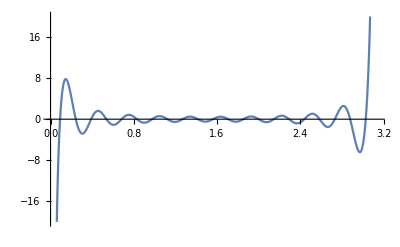

```mathematica
Plot[Gegenbauer[x],{x,0,π},PlotRange->{-20,20}]
```

```mathematica
n+λ-1/2
```

21

# Toy Model SO(2)->SO(1)

```mathematica
Clear[λ,Rotation,V0,V,ϕvec];
```

```mathematica
Rotation={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
ϕvec={ϕ1,ϕ2};
V0[ϕ11_,ϕ22_]:=(-m^2/2 ϕvec.ϕvec+λ/4 (ϕvec.ϕvec)^2)/.{ϕ1->ϕ11,ϕ2->ϕ22};
VGB[ϕ11_,ϕ22_]:=ϵ M^2/2 ϕ1^2/.{ϕ1->ϕ11,ϕ2->ϕ22};
```

```mathematica
(*FullSimplify[(φ1^2-φ2^2)/.{φ1->(Rotation.ϕvec)[[1]],φ2->(Rotation.ϕvec)[[2]]}]*)
```

```mathematica
Clear[λ];λ=m^2/f^2;
```

```mathematica
(D[V0[ϕ1,ϕ2]+VGB[ϕ1,ϕ2],{ϕ1,2}])/.{ϕ1->0,ϕ2->f}
```

M^2 ϵ

```mathematica
Rotation1={{Cos[θ1],Sin[θ1]},{-Sin[θ1],Cos[θ1]}};
Rotation2={{Cos[θ2],Sin[θ2]},{-Sin[θ2],Cos[θ2]}};
FullSimplify[Rotation1.Rotation2]
```

{{Cos[θ1+θ2],Sin[θ1+θ2]},{-Sin[θ1+θ2],Cos[θ1+θ2]}}

# Toy Model SO(3)->SO(2)

```mathematica
ClearAll["Global`*"];
Clear[m,f,λ,Rotation,V0,V,ϕvec,m,M];Rotationz={{Cos[θz],Sin[θz],0},{-Sin[θz],Cos[θz],0},{0,0,1}};
Rotationy={{Cos[θy] ,0,Sin[θy]},{0,1,0},{-Sin[θy],0,Cos[θy]}};
Rotationx={{1,0,0},{0,-Sin[θx],Cos[θx]},{0,Cos[θx],Sin[θx]}};
RotationFull=FullSimplify[Rotationz.Rotationx.Rotationy];
ϕvec={ϕ1,ϕ2,ϕ3};πvec={ϕ1,ϕ2};V0[ϕ11_,ϕ22_,ϕ33_]:=(-m^2/2 ϕvec.ϕvec+λ/4 (ϕvec.ϕvec)^2)/.{ϕ1->ϕ11,ϕ2->ϕ22,ϕ3->ϕ33};
VGB[ϕ11_,ϕ22_,ϕ33_]:=ϵ (-M^2πvec.πvec+λπ (πvec.πvec)^2)/.{ϕ1->ϕ11,ϕ2->ϕ22,ϕ3->ϕ33};
minimizationCondition=FullSimplify[Table[D[V0[π1,π2,σ]+VGB[π1,π2,σ],{π1,π2,σ}[[i]]]/.{σ->f,π1->v Sin[α],π2->v Cos[α]},{i,1,3}]];
```

```mathematica
λ=λ/.Solve[minimizationCondition[[3]]==0,λ][[1]];λπ=λπ/.Solve[minimizationCondition[[1]]==0,λπ][[1]];
```

```mathematica
massmatrix[i_,j_]:=D[D[V0[π1,π2,σ]+VGB[π1,π2,σ],{π1,π2,σ}[[i]]],{π1,π2,σ}[[j]]];
massmatTable=FullSimplify[Table[massmatrix[i,j],{i,1,3},{j,1,3}]];
```

```mathematica
MatrixForm[FullSimplify[massmatTable/.{π1->Π Sin[α],π2->Π Cos[α]}]]
```

(-(2 M^2 ϵ (v^2-2 Π^2+Π^2 Cos[2 α]))/v^2-(m^2 (f^2+v^2-2 Π^2-σ^2+Π^2 Cos[2 α]))/(f^2+v^2) | (m^2/(f^2+v^2)+(2 M^2 ϵ)/v^2) Π^2 Sin[2 α] | (2 m^2 Π σ Sin[α])/(f^2+v^2)
(m^2/(f^2+v^2)+(2 M^2 ϵ)/v^2) Π^2 Sin[2 α] | (2 M^2 ϵ (-v^2+2 Π^2+Π^2 Cos[2 α]))/v^2+(m^2 (-f^2-v^2+2 Π^2+σ^2+Π^2 Cos[2 α]))/(f^2+v^2) | (2 m^2 Π σ Cos[α])/(f^2+v^2)
(2 m^2 Π σ Sin[α])/(f^2+v^2) | (2 m^2 Π σ Cos[α])/(f^2+v^2) | -(m^2 (f^2+v^2-Π^2-3 σ^2))/(f^2+v^2))

```mathematica
relevantMassmat=Table[(massmatTable/.{σ->f,π1->v Sin[0],π2->v Cos[0]})[[i]][[j]],{i,2,3},{j,2,3}];MatrixForm[relevantMassmat]
```

((2 m^2 v^2)/(f^2+v^2)+4 M^2 ϵ | (2 f m^2 v)/(f^2+v^2)
(2 f m^2 v)/(f^2+v^2) | (2 f^2 m^2)/(f^2+v^2))

```mathematica
detMatrix=Det[relevantMassmat];trMatrix=FullSimplify[Tr[relevantMassmat]];
```

```mathematica
FullSimplify[(trMatrix+√(trMatrix^2-4detMatrix))/2]
```

m^2+2 M^2 ϵ+√(-(8 f^2 m^2 M^2 ϵ)/(f^2+v^2)+(m^2+2 M^2 ϵ)^2)

```mathematica
Series[(trMatrix-√(trMatrix^2-4detMatrix))/2,{f,Infinity,3}]
```

(m^2+2 M^2 ϵ-√((m^2-2 M^2 ϵ)^2))-(4 (m^2 M^2 v^2 ϵ))/(√((m^2-2 M^2 ϵ)^2) f^2)+O[1/f]^4

```mathematica
FieldDependentMasses=FullSimplify[Eigenvalues[massmatTable/.{π1->Π Sin[α],π2->Π Cos[α]}]];
```

```mathematica
FullSimplify[FieldDependentMasses/.{Π->v,σ->f}]
```

{0,m^2+2 M^2 ϵ-(√(v^4 (m^4 (f^2+v^2)^2+4 m^2 M^2 (-f^4+v^4) ϵ+4 M^4 (f^2+v^2)^2 ϵ^2)))/(v^2 (f^2+v^2)),m^2+2 M^2 ϵ+(√(v^4 (m^4 (f^2+v^2)^2+4 m^2 M^2 (-f^4+v^4) ϵ+4 M^4 (f^2+v^2)^2 ϵ^2)))/(v^2 (f^2+v^2))}

```mathematica
Clear[ϵ,M,m,f,v,α];
ϵ=10^(-9);m=4;M=500;f=4000;v=100;α=π/2;
Print["λ_π=",N[λπ],", λ=",N[λ]]
Print[MatrixForm[N[massmatTable/.{σ->f,π1->v Sin[α],π2->v Cos[α]}]]]
N[Eigenvalues[massmatTable/.{σ->f,π1->v Sin[α],π2->v Cos[α]}]]
```

λ_π=12.5, λ=9.99375×10^-7

(0.0209875 | 0. | 0.7995
0. | 0. | 0.
0.7995 | 0. | 31.98)

{32.,0.000999375,0.}

```mathematica
{2m^2,4M^2 ϵ}
```

{32,1/1000}

```mathematica
ContourPlot[V0[Π Cos[10],Π Sin[10],σ]+VGB[Π Cos[10],Π Sin[10],σ],{σ,0,1.2f},{Π,0,1.2f}]
```

-Graphics-

```mathematica
VCW[h_?NumericQ,s_?NumericQ]:=Module[{μR=f,listmasses=Sort[N[FieldDependentMasses/.{Π->h,σ->s}]]},(*Print["The field depdent thermal masses are ",listmasses," (GeV)^2"];*)
VCWout=Sum[Re[If[listmasses[[i]]!=0,listmasses[[i]]^2 Log[listmasses[[i]]/μR^2],0]],{i,1,3}];
Return[VCWout]];
```

```mathematica
D[V0[0,h,s]+VGB[0,h,s]+VCW[h,s],h]/.{h->v 1.,s->f 1.}
```

-0.484432

```mathematica
Clear[VCT,SolCTs];

VCT[ϕ11_,ϕ22_,ϕ33_]:=(-δm/2 ϕvec.ϕvec+δλ/4 (ϕvec.ϕvec)^2)/.{ϕ1->ϕ11,ϕ2->ϕ22,ϕ3->ϕ33};
```

```mathematica
D[VCW1[h,s]+VCT[0,h,s],h]/.{h->v,s->f}
```

-100 δm+1601000000 δλ+VCW1^(1,0)[100,4000]

```mathematica
onshell1=D[VCW1[h,s]+VCT[0,h,s],h]/.{h->f};
onshell2=D[VCW1[h]+VCT[0,0,h],{h,2}]/.{h->f};
```

```mathematica
SolCTs=Solve[{onshell1==0,onshell2==0},{δm,δλ}];
```

```mathematica
SolCTs
```

{{δm→-(-16000000 VCW1''[4000]-s^2 VCW1''[4000]+12000 VCW1^(1,0)[4000,s])/(-32000000+s^2),δλ→-(-4000 VCW1''[4000]+VCW1^(1,0)[4000,s])/(4000 (-32000000+s^2))}}

Equation C1a from Dolan and Jackiw

```mathematica
JB[a_]:=x^2Log[1-Exp[-√(x^2+a/T^2)]];
JBtotal=Map[JB,FieldDependentMasses];
VT[hh_,TT_]:=TT^4/(2 π^2)NIntegrate[Re[Sum[JBtotal[[i]],{i,1,3}]/.{h->hh,T->TT}],{x,0,Infinity}];
```

```mathematica
FieldDependentMasses
```

{(16000000 (-160000+(-10000+Π^2)/2000)+10000 (-(32001 (100-Π) (100+Π))/2000+16 σ^2))/160100000000,1/160100000000(-1600025000+16000000 (-320005/2+(3 Π^2)/4000)-√((40025000-(344015 Π^2)/2)^2+320000 (40025000+(295985 Π^2)/2) σ^2+25600000000 σ^4)+10000 ((3 Π^2)/4000+32 (Π^2+σ^2))),1/160100000000(-1600025000+16000000 (-320005/2+(3 Π^2)/4000)+√((40025000-(344015 Π^2)/2)^2+320000 (40025000+(295985 Π^2)/2) σ^2+25600000000 σ^4)+10000 ((3 Π^2)/4000+32 (Π^2+σ^2)))}

```mathematica
Vtot[h_,T_]:=Evaluate[(V0[h,0,0]+VCW[h]+VT[h,T])]
```

NIntegrate::inumr: The integrand Re[x^2 Log[1-ⅇ^Times[«2»]]+x^2 Log[1-ⅇ^Times[«2»]]+x^2 Log[1-ⅇ^Times[«2»]]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

# My tensor calculus

```mathematica
ClearAll["Global`*"]
```

```mathematica
Npi=10;
pivec=Table[pi[i],{i,1,Npi}];
Pinorm=√(pivec.pivec);
gmetric=Table[KroneckerDelta[a,b]+pi[a]pi[b]/(F^2-pivec.pivec),{a,1,Npi},{b,Npi}];gmetricinverse=Table[KroneckerDelta[a,b]-pi[a]pi[b]/F^2,{a,1,Npi},{b,Npi}];
Print["Check g times g^-1"]
MatrixForm[FullSimplify[gmetric.gmetricinverse]]
dgilk=Hold[Sum[gmetricinverse[[i,m]](D[gmetric[[l,m]],pi[k]]+D[gmetric[[k,m]],pi[l]]-D[gmetric[[l,k]],pi[m]]),{m,1,Npi}]];Christoffel=1/2Table[ReleaseHold[dgilk],{i,1,Npi},{l,1,Npi},{k,1,Npi}];
Potential=-c √(F^2-pivec.pivec);
Potential=G[Pinorm];
gD2V=Hold[Sum[gmetricinverse[[i,k]]D[Potential,pi[k],pi[j]],{k,1,Npi}]];
gGamDV=Hold[Sum[gmetricinverse[[i,l]] Christoffel[[m,j,l]]D[Potential,pi[m]],{m,1,Npi},{l,1,Npi}]];MassMatrix=Table[ReleaseHold[gD2V-gGamDV],{i,1,Npi},{j,1,Npi}];
```

Check g times g^-1

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Replace[FullSimplify[Tr[MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(-F^2+Sum[pi[i]^2,{i,1,Npi}])->-F^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

(((9 F^2-10 Π^2) G'[√(Π^2)])/(√(Π^2))-(-F^2+Π^2) G''[√(Π^2)])/F^2

```mathematica
DSolve[{G''[Π](-Π^2/F^2+1)+G'[Π](2F^2-3Π^2)/Π/F^2==constant G[Π]},G[Π],Π]
```

{{G[Π]→ⅇ^(1/2 (-2 Log[Π]+1/2 Log[-F^2+Π^2])) C[1] LegendreP[1/2 (-1+2 √(1-constant F^2)),1/2,Π/F]+ⅇ^(1/2 (-2 Log[Π]+1/2 Log[-F^2+Π^2])) C[2] LegendreQ[1/2 (-1+2 √(1-constant F^2)),1/2,Π/F]}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
Npi=3;
pivec=Table[pi[i],{i,1,Npi}];
Pinorm=√(pivec.pivec);gmetric=Sin[Pinorm/f]^2 f^2/Pinorm^2 Table[KroneckerDelta[a,b]+pi[a]pi[b]/Pinorm^2((Pinorm^2/f^2)Csc[Pinorm/f]^2-1),{a,1,Npi},{b,Npi}];
gmetricinverse=1/(Sin[Pinorm/f]^2) Pinorm^2 /f^2Table[KroneckerDelta[a,b]-pi[a]pi[b]/Pinorm^2(1-f^2/Pinorm^2 Sin[Pinorm/f]^2),{a,1,Npi},{b,Npi}];
```

```mathematica
Print["Check g times g^-1"]
MatrixForm[FullSimplify[gmetric.gmetricinverse]]
```

Check g times g^-1

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
dgilk=Hold[Sum[gmetricinverse[[i,m]](D[gmetric[[l,m]],pi[k]]+D[gmetric[[k,m]],pi[l]]-D[gmetric[[l,k]],pi[m]]),{m,1,Npi}]];Christoffel=1/2Table[ReleaseHold[dgilk],{i,1,Npi},{l,1,Npi},{k,1,Npi}];
```

```mathematica
Potential=G[Pinorm/f];gD2V=Hold[Sum[gmetricinverse[[i,k]]D[Potential,pi[k],pi[j]],{k,1,Npi}]];
gGamDV=Hold[Sum[gmetricinverse[[i,l]] Christoffel[[m,j,l]]D[Potential,pi[m]],{m,1,Npi},{l,1,Npi}]];MassMatrix=Table[ReleaseHold[gD2V-gGamDV],{i,1,Npi},{j,1,Npi}];
```

```mathematica
Replace[ FullSimplify[Tr[MassMatrix]],√(pi[1]^2+pi[2]^2+pi[3]^2)->Π,All]
```

(2 Cot[Π/f] G'[Π/f]+G''[Π/f])/f^2

# Toy Model Gaillard

```mathematica
(*This is the case of Gaillard!*)
ClearAll["Global`*"];
ϕvec={ϕ1,ϕ2,ϕ3};
πvec={ϕ1,ϕ2};
V0[ϕ11_,ϕ22_,ϕ33_]:=λ( ϕvec.ϕvec-f^2)^2/.{ϕ1->ϕ11,ϕ2->ϕ22,ϕ3->ϕ33};
VGBGaillard[ϕ11_,ϕ22_,ϕ33_]:=c √(f^2-πvec.πvec)/.{ϕ1->ϕ11,ϕ2->ϕ22,ϕ3->ϕ33};
minimizationConditionGaillard=FullSimplify[Table[D[V0[π1,π2,σ]+VGBGaillard[π1,π2,σ],{π1,π2,σ}[[i]]]/.{σ->f,π1->0v Sin[α],π2->0v Cos[α]},{i,1,3}]];
massmatrixGaillard[i_,j_]:=D[D[V0[π1,π2,σ]+VGBGaillard[π1,π2,σ],{π1,π2,σ}[[i]]],{π1,π2,σ}[[j]]];
massmatTableGaillard=FullSimplify[Table[massmatrixGaillard[i,j],{i,1,3},{j,1,3}]];
MatrixForm[FullSimplify[massmatTableGaillard/.{σ->f,π1->0v Sin[α],π2->0v Cos[α]}]]
```

(-c/(√(f^2)) | 0 | 0
0 | -c/(√(f^2)) | 0
0 | 0 | 8 f^2 λ)

```mathematica
minimizationConditionGaillard
```

{0,0,0}

```mathematica
Clear[c,f,λ];
f=1000;λ=1;c=-10^3;Nc=2;
Print["Masses are given by"]
Print[MatrixForm[N[massmatTableGaillard/.{σ->f,π1->0v Sin[α],π2->0v Cos[α]}]]]
```

Masses are given by

(1. | 0. | 0.
0. | 1. | 0.
0. | 0. | 8.×10^6)

Tree level potential in the UV

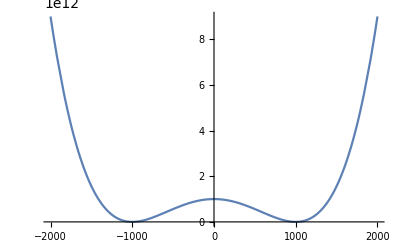

```mathematica
Print["Tree level potential in the UV"];Plot[V0[0,0,σ]+VGBGaillard[0,0,σ],{σ,-2000,2000}]
```

```mathematica
(*Field dependent mass with an artificial minus sign to make it positive*)
α=-(Nc c/f^2)√(f^2-φ^2)/T^2;
```

```mathematica
Coefficient[FullSimplify[Normal[Series[VGBGaillard[φ,0,0]+T^4/2/π^2(-π^4/45+π^2/12 α-π/6 α^(3/2)),{φ,0,5}]],Assumptions->{F>0,Nc>0,T>0,c<0}],φ^2]
```

(288000000000000 π+72000000 √2 T-24000000 π T^2)/(576000000000000 π)

```mathematica
N[Solve[%==0,T]]
```

{{T→-3463.43},{T→3464.78}}

```mathematica
VT[ππ_,TT_]:=Module[{expressionOut=Normal[FullSimplify[Series[VGBGaillard[φ,0,0]+T^4/2/π^2(-π^4/45+π^2/12 α-π/6 α^(3/2)),{φ,0,5}],Assumptions->{1/F>0,Nc>0,T>0}]]},
(*Print[expressionOut]*)(*Print[Normal[Series[α,{φ,0,4}]]/.{φ->ππ,T->TT}]*)Return[N[expressionOut/.{φ->ππ,T->TT}]]]
```

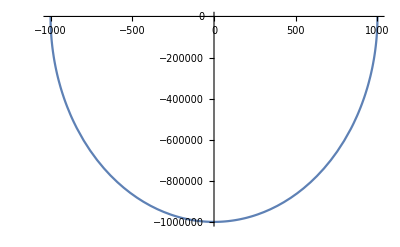

```mathematica
Plot[VGBGaillard[φ,0,0],{φ,-f,f}]
```

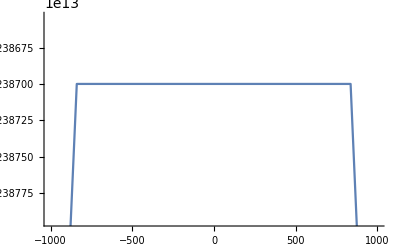

```mathematica
Plot[VT[x,√12. f+1],{x,-f/1,f/1}]
```

```mathematica
(*This is the case of Gaillard!*)
ClearAll["Global`*"];
ϕvec={ϕ1,ϕ2,ϕ3};
πvec={ϕ1,ϕ2};
V0[ϕ11_,ϕ22_,ϕ33_]:=μ^2/2ϕvec.ϕvec+λ/4!( ϕvec.ϕvec)^2/.{ϕ1->ϕ11,ϕ2->ϕ22,ϕ3->ϕ33};
VGBGaillard[ϕ11_,ϕ22_,ϕ33_]:=c ϕ3/.{ϕ1->ϕ11,ϕ2->ϕ22,ϕ3->ϕ33};
```

```mathematica
FullSimplify[Table[D[V0[π1,π2,σ]+VGBGaillard[π1,π2,σ],{π1,π2,σ}[[i]]]/.{σ->f,π1->0v Sin[α],π2->0v Cos[α]},{i,1,3}]]
```

{0,0,c+(f^3 λ)/6+f μ^2}

```mathematica
Coefficient[Expand[V0[0,0,σ+f]+VGBGaillard[0,0,σ+f]],σ^3]
```

(f λ)/6

```mathematica
minimizationConditionGaillard=FullSimplify[Table[D[V0[π1,π2,σ]+VGBGaillard[π1,π2,σ],{π1,π2,σ}[[i]]]/.{σ->f,π1->0v Sin[α],π2->0v Cos[α]},{i,1,3}]];
massmatrixGaillard[i_,j_]:=D[D[V0[π1,π2,σ]+VGBGaillard[π1,π2,σ],{π1,π2,σ}[[i]]],{π1,π2,σ}[[j]]];
massmatTableGaillard=FullSimplify[Table[massmatrixGaillard[i,j],{i,1,3},{j,1,3}]];
MatrixForm[FullSimplify[massmatTableGaillard/.{σ->f,π1->0v Sin[α],π2->0v Cos[α]}]]
```

```mathematica
FullSimplify[TrigExpand[2(p/f Cot[p/f]-1)+Tan[p/f]^2+(p/f Cot[p/f]-1)^2+2Tan[p/f]^2(p/f Cot[p/f]-1)+Tan[p/f]^2(p/f Cot[p/f]-1)^2]]
```

-1+(p^2 Csc[p/f]^2)/f^2

# Gauge covariant derivative

```mathematica
Clear[SU2];SU2=I/2 {{g W3+g1 B,g W1-I g W2},{g W1+I g W2,-g W3+ g1 B}}.{ϕ2+I ϕ1,ϕ4-I ϕ3};
```

```mathematica
FullSimplify[ComplexExpand[Conjugate[SU2]].SU2]
```

1/4 (B^2 g1^2 (ϕ1^2+ϕ2^2+ϕ3^2+ϕ4^2)+g^2 (W1^2+W2^2+W3^2) (ϕ1^2+ϕ2^2+ϕ3^2+ϕ4^2)-2 B g g1 (2 (W1 ϕ1 ϕ3+W2 ϕ2 ϕ3+W2 ϕ1 ϕ4-W1 ϕ2 ϕ4)+W3 (-ϕ1^2-ϕ2^2+ϕ3^2+ϕ4^2)))

```mathematica
Clear[O4];O4=1/2 {{0,g W3+g1 B,-g W2,g W1},{-g W3-g1 B,0,g W1, g W2},{g W2, -g W1,0,g W3-g1 B},{-g W1,-g W2, -g W3+g1 B ,0}}.{ϕ1,ϕ2,ϕ3,ϕ4};
```

```mathematica
FullSimplify[ComplexExpand[Conjugate[O4]].O4]
```

1/4 (B^2 g1^2 (ϕ1^2+ϕ2^2+ϕ3^2+ϕ4^2)+g^2 (W1^2+W2^2+W3^2) (ϕ1^2+ϕ2^2+ϕ3^2+ϕ4^2)-2 B g g1 (2 (W1 ϕ1 ϕ3+W2 ϕ2 ϕ3+W2 ϕ1 ϕ4-W1 ϕ2 ϕ4)+W3 (-ϕ1^2-ϕ2^2+ϕ3^2+ϕ4^2)))

```mathematica
FullSimplify[ComplexExpand[Conjugate[SU2]].SU2-ComplexExpand[Conjugate[O4]].O4]
```

0

```mathematica
Clear[ϕvec,ϕvecPolar];
ϕvec={ϕ1,ϕ2,ϕ3,ϕ4};ϕvecPolar=ϕvec/.{ϕ1->(f+h)Sin[θ]Cos[ϕ] Sin[ψ],ϕ2->(f+h)Sin[θ]Sin[ϕ]Sin[ψ],ϕ3->(f+h)Cos[θ]Sin[ψ],ϕ4->(f+h)Cos[ψ]};
```

```mathematica
x=R Sin[θ]Cos[ϕ] Sin[ψ];
y=R Sin[θ]Sin[ϕ]Sin[ψ];
z=R Cos[θ]Sin[ψ]
zz=R Cos[ψ];
```

R Cos[θ] Sin[ψ]

```mathematica
FullSimplify[Det[Table[D[{x,y,z,zz}[[i]],{θ,ϕ,ψ,R}[[j]]],{i,1,4},{j,1,4}]]]
```

R^3 Sin[θ] Sin[ψ]^2

```mathematica
Integrate[Sin[θ] Sin[ψ]^2,{θ,0,π},{ψ,0,π},{ϕ,0,2π}]
```

2 π^2

```mathematica
Gamma[2]
```

1

```mathematica
2 π^(2)/Gamma[2]
```

2 π^2

```mathematica
ϕvecPolar/.{θ->0,ψ->0}
```

{0,0,0,f+h}

```mathematica
FullSimplify[ϕvecPolar.ϕvecPolar]
```

(f+h)^2

```mathematica
FullSimplify[ϕvecPolar.{{0,g W3+g1 B,-g W2,g W1},{-g W3-g1 B,0,g W1, g W2},{g W2, -g W1,0,g W3-g1 B},{-g W1,-g W2, -g W3+g1 B ,0}}.ϕvecPolar]
```

0

```mathematica
MatrixForm[{{0,g W3+g1 B,-g W2,g W1},{-g W3-g1 B,0,g W1, g W2},{g W2, -g W1,0,g W3-g1 B},{-g W1,-g W2, -g W3+g1 B ,0}}]
```

(0 | B g1+g W3 | -g W2 | g W1
-B g1-g W3 | 0 | g W1 | g W2
g W2 | -g W1 | 0 | -B g1+g W3
-g W1 | -g W2 | B g1-g W3 | 0)

ReplaceAll::reps: {sols} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

# Renormalization of simple SSB potential

```mathematica
Clear[V0,λ,VCW,m,a,b];
V0[ϕ_]:=-m^2/2 ϕ^2+λ ϕ^4/4;VCW[ϕ_]:=(-m^2+3λ ϕ^2)^2/64/π^2(Log[(-m^2+3 λ ϕ^2)/μ^2]-1/2);
VCT[ϕ_]:=a ϕ^2+b ϕ^4;
ren1=D[V0[ϕ]+VCW[ϕ]+VCT[ϕ],{ϕ,2}]/.{ϕ->M};
ren2=D[V0[ϕ]+VCW[ϕ]+VCT[ϕ],{ϕ,4}]/.{ϕ->M};
{a,b}={a,b}/.Solve[{ren1==μr^2,ren2==λr},{a,b}][[1]];
```

```mathematica
FullSimplify[(V0[ϕ]+VCW[ϕ]+VCT[ϕ])/.{M->0}]
```

(-3 m^4+6 (3 m^2 λ+32 π^2 μr^2) ϕ^2+(-81 λ^2+16 π^2 λr) ϕ^4+18 λ ϕ^2 (2 m^2-3 λ ϕ^2) Log[-m^2/μ^2]+6 (m^2-3 λ ϕ^2)^2 Log[-(m^2-3 λ ϕ^2)/μ^2])/(384 π^2)

```mathematica
FullSimplify[VCT[ϕ]/.{M->0}]
```

(ϕ^2 (96 π^2 (m^2+μr^2)+(-27 λ^2+8 π^2 (-6 λ+λr)) ϕ^2+9 λ (2 m^2-3 λ ϕ^2) Log[-m^2/μ^2]))/(192 π^2)

# On-shell renormalization in dim-reg

```mathematica
Clear[V0,VCW,VCT,λ,mh,m,v,μ,a,b,OnShell1,OnShell2];
V0[ϕ_]:=-m^2/2 ϕ^2+λ ϕ^4/4;VCW[ϕ_]:=(-m^2+3λ ϕ^2)^2/64/π^2(Log[(-m^2+3 λ ϕ^2)/μ^2]-1/2);
VCT[ϕ_]:=a ϕ^2+b ϕ^4;
λ=λ/.Solve[(D[V0[ϕ],ϕ]/.{ϕ->v})==0,λ][[1]];
m=m/.Solve[(D[V0[ϕ],{ϕ,2}]/.{ϕ->v})==mh^2,m][[1]];
OnShell1=D[VCW[ϕ]+VCT[ϕ],{ϕ,1}]/.{ϕ->v};
OnShell2=D[VCW[ϕ]+VCT[ϕ],{ϕ,2}]/.{ϕ->v};
{a,b}={a,b}/.Solve[{OnShell1==0,OnShell2==0},{a,b}][[1]];
VOnShell=1/64/π^2((-m^2+3 λ ϕ^2)^2(Log[(-m^2+3 λ ϕ^2)/mh^2]-3/2)+2 (-m^2+3 λ ϕ^2)mh^2);
```

```mathematica
FullSimplify[b]
```

-(9 mh^4 (1+Log[mh^2/μ^2]))/(256 π^2 v^4)

```mathematica
FullSimplify[ExpandAll[VCW[ϕ]+VCT[ϕ]+VOnShell]]
```

(mh^4 (-6 v^4+42 v^2 ϕ^2-27 ϕ^4+(6 v^2 ϕ^2-9 ϕ^4) Log[mh^2/μ^2]+(v^2-3 ϕ^2)^2 (Log[-(mh^2 (v^2-3 ϕ^2))/(2 v^2 μ^2)]+Log[-1/2+(3 ϕ^2)/(2 v^2)])))/(256 π^2 v^4)

# On-shell renormalization in cutoff-reg

```mathematica
Clear[V0,VCW,δ,VCT,Λ,λ,mh,m,v,μ,a,b,OnShell1,OnShell2];
V0[ϕ_]:=-m^2/2 ϕ^2+λ ϕ^4/4+m^4/λ/4;VCW[ϕ_]:=(-m^2+3λ ϕ^2)^2/64/π^2(Log[(-m^2+3 λ ϕ^2)/Λ^2]-1/2)+1/64/π^2 2Λ^2 (-m^2+3λ ϕ^2);
VCT[ϕ_]:=a ϕ^2+b ϕ^4+δ;
λ=λ/.Solve[(D[V0[ϕ],ϕ]/.{ϕ->v})==0,λ][[1]];
m=m/.Solve[(D[V0[ϕ],{ϕ,2}]/.{ϕ->v})==mh^2,m][[1]];
OnShell1=D[VCW[ϕ]+VCT[ϕ],{ϕ,1}]/.{ϕ->v};
OnShell2=D[VCW[ϕ]+VCT[ϕ],{ϕ,2}]/.{ϕ->v};
{a,b}={a,b}/.Solve[{OnShell1==0,OnShell2==0},{a,b}][[1]];
VOnShell=1/64/π^2((-m^2+3 λ ϕ^2)^2(Log[(-m^2+3 λ ϕ^2)/mh^2]-3/2)-2 (-m^2+3 λ ϕ^2)mh^2);
δ=δ/.Solve[VCW[v]+VCT[v]==0,δ][[1]];ΛCT=VOnShell/.{ϕ->v};
```

```mathematica
FullSimplify[(V0[ϕ]+VCW[ϕ]+VCT[ϕ])/.{ϕ->v}]
```

0

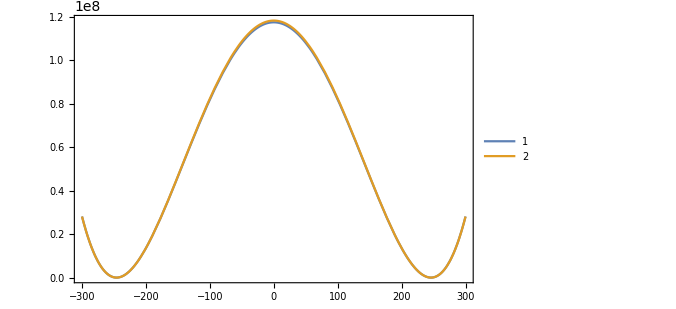

-Graphics-

```mathematica
Clear[mh,v,Λ]
mh=125;
v=246;
Λ=1000;
Plot[{Re[N[V0[ϕ]+VCW[ϕ]+VCT[ϕ]]],V0[ϕ]},{ϕ,-300,300}]
```